```mathematica
<<ACPackages`
```

```mathematica
SetWorkDir["2009.08.07"]
```

d:\home\Anton\programs\tor2d\2009.08.07

```mathematica
SetWorkDir["2009.11.12\\Re1"]
```

D:\Home\Anton\programs\tor2d\2009.11.12\Re1

```mathematica
SetWorkDir["Run"]
```

d:\home\Anton\programs\tor2D\Run

```mathematica
SetDirectory["d:\\home\\anton\\programs\\tor2d\\tor\\Debug"]
```

d:\home\anton\programs\tor2d\tor\Debug

```mathematica
SetWorkDir["tor2d/Debug"]
```

D:\programs\icmm\tor2D\tor2d\Debug

```mathematica
AverageTimeProfil[l_List,t_,dt_:1]:=Apply[Plus,#]/Length[#]&[Map[#[[2]]&,Select[lv,(t≤#[[1]][[1]]<t+dt)&]]];
UnsortedUnion[x_,ndig_:4]:=N[Reap[Sow[1,Round[10^ndig x]],_,#1&]⟦2⟧10^-ndig];
```

## Общие тенденции

```mathematica
Off[Thread::tdlen];
lv=ReadList["vv.dat"];lv=Map[{#⟦1,1⟧,#⟦2⟧}&,lv];
ltm=Flatten[First/@lv];
{Length[ltm],Last[ltm]}
```

{2517,2.60616}

```mathematica
Scan[Print[PrintRange[#,{0,0.007}]]&,CutList[WithoutFict[#[[2]],3]&/@lv,20]]
```

```mathematica
ListPlot[{First[#],Max[WithoutFict@Last[#]]}&/@lv]
```

```mathematica
Export["energy0.dat",Transpose@Join[{ltm},len⟦All,2⟧,Map[Last,{mp,mdp,mvx,mdvx,mvy,mdvy,mvz,mdvz,qp,qvx,qvy,qvz},{2}]]]
```

```mathematica
Export["energy0.dat",Transpose[len]]
```

energy0.dat

```mathematica
Dimensions/@{ltm,len,mp}
```

{{78394},{14,78394},{78394,2}}

```mathematica
FileNames["en*"]
```

{energy.dat}

Import["en.zip", "energy.dat", "Elements" -> "Table"]
Import["energy.dat", "Table"]

```mathematica
len=Transpose[Fold[If[#2⟦1⟧>#1⟦-1,1⟧,Append[#1,#2],#1]&,{First[Transpose[len]]},Transpose[len]]];
```

```mathematica
Dynamic[Refresh[{
len=Transpose[Select[Import["energy.dat","Table"],0<First[#]&]];
ltm=First[len];
PrintRange[dif[Union[ltm]],All,PlotLabel->{20Length[ltm],Last[ltm]}],
{mp,mdp,mvx,mdvx,mvy,mdvy,mvz,mdvz,qp,qvx,qvy,qvz}=Union[Transpose[{ltm,#}]]&/@Drop[len,2];
PrintRange[{#⟦1⟧/3,Log[10,#⟦2⟧]}&/@(qvx+qvy+qvz),Automatic,PlotLabel->√((qvx+qvy+qvz)⟦-1,-1⟧)]}
,UpdateInterval->5]]
```

```mathematica
len=Transpose[Select[Import["energy.dat","Table"],0<First[#]<100&]];
ltm=First[len];PrintRange[dif[Union[ltm]],All,PlotLabel->{100Length[ltm],Last[ltm]}]
{mp,mdp,mvx,mdvx,mvy,mdvy,mvz,mdvz,qp,qvx,qvy,qvz}=Union[Transpose[{ltm,#}]]&/@Drop[len,2];
PrintRange[{#⟦1⟧/3,Log[10,#⟦2⟧]}&/@(qvx+qvy+qvz),Automatic,PlotLabel->√((qvx+qvy+qvz)⟦-1,-1⟧)]
```

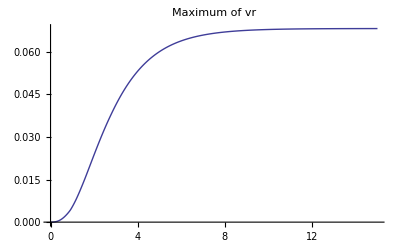
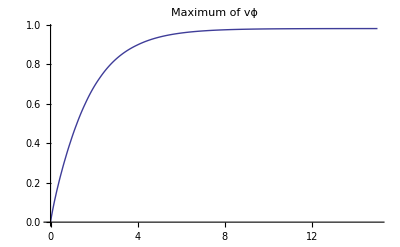
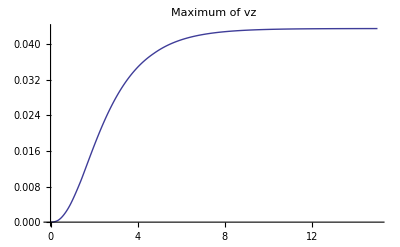
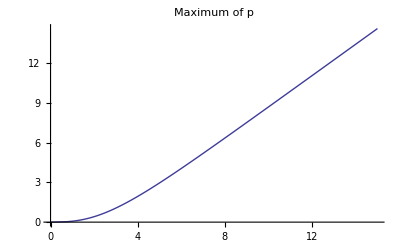

```mathematica
MapThread[PrintRange[#1,Automatic,PlotLabel->#2]&,{Map[{#⟦1⟧,10^Log[10,#⟦2⟧]}&,{mvx,mvy,mvz,mp},{2}],{"Maximum of vr","Maximum of vϕ","Maximum of vz","Maximum of p"}}]
```

```mathematica
Smooth[l_,part_:0.02]:=MovingAverage[l,⌈part Length[l]⌉]
```

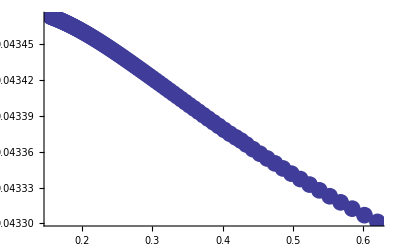
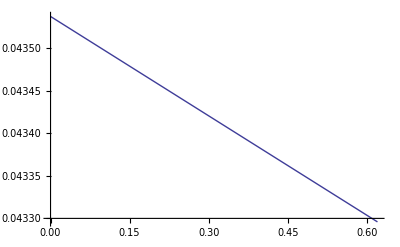

HoelderError=0.0000252767

degree of hyperbole=1

0.0435371

```mathematica
ListLimit[Take[mvz,-Min[100,Length[mvy]]]//Smooth,CutValues->False,UseShift->True,ApproximationReport->{MaxError,HoelderError,LimitPlot,PolynomDegree}]
```

```mathematica
ListPlot[{1/(First[#]-685),Last[#]}&/@Take[mvy,-1000],PlotRange->{{0,Automatic},All}]
```

```mathematica
ListPlot[Take[mvy,-2000]//Smooth]
```

```mathematica
{maxvx,maxvy,maxvz,mqvx,mqvy,mqvz}=ListLimit[Take[Smooth[#],-Min[100,Length[mvy]]],CutValues->False,UseShift->True,ApproximationReport->{MaxError,HoelderError}]&/@{mvx,mvy,mvz,qvx,qvy,qvz}
```

HoelderError=0.0000506589

HoelderError=0.000259039

HoelderError=0.0000292779

HoelderError=9.29004×10^-7

HoelderError=0.00013002

HoelderError=3.20622×10^-7

{0.0683114,0.981466,0.0435443,0.000631481,0.246983,0.000219645}

```mathematica
MapThread[PrintRange[#1,Automatic,PlotLabel->#2]&,{Map[{#⟦1⟧,10^Log[10,#⟦2⟧]}&,{qvx,qvy,qvz,qp},{2}],{"Mean quadratic of vr","Mean quadratic of vϕ","Mean quadratic of vz","Mean quadratic of p"}}]
```

```mathematica
MapThread[PrintRange[#1,All,PlotLabel->#2]&,{Map[{#⟦1⟧,Log[10,#⟦2⟧]}&,{mdvx,mdvy,mdvz,mdp},{2}],{"Max difference of vr","Max difference vϕ","Max difference of vz","Max difference of p"}}]
```

## Обработка массивов

```mathematica
dump=Release[ReadList["pumpflow.dmp",Hold[Expression]]/.{a_+E*b_->b*10^a}];
{coor,bounds}=ReadAuxFiles2D[{"coord"},ShiftVector->{0,0},ProcDistrib->{2,2},NumberOfRefs->2];
```

Set::write: Tag Times in current time is Protected.

Set::write: Tag Times in current iteration is Protected.

Set::write: Tag Times in along axes number of processors is Protected.

General::stop: Further output of Set will be suppressed during this calculation.

```mathematica
Max/@Drop[dump,6]
```

{242410.,1.3967×10^14,8.4788×10^11,1.0497×10^13,0.01,3322.2,56.909,0.35899,57.579,0.01}

```mathematica
GetInner[ar_?ArrayQ]:=Block[{b},Switch[Length[Dimensions[ar]],3,Transpose[(node/.b_:>BitAnd[b,8])/8#&/@Transpose[ar]],2,(node/.b_:>BitAnd[b,8])/8 ar,_,$Failed]]
```

```mathematica
ReadDrawSection["pumpflow(0.5).snp",Text2D,5]
```

```mathematica
{p,vx,vy,vz,nut}=ReadTextSnapFile2D["pumpflow_2_963993.snp",5,PrintInfo->Automatic];
{coor,bounds,node}=ReadAuxFiles2D[{"coord","node"},ShiftVector->{0,0},ProcDistrib->{1,2},NumberOfRefs->2];
Print[bounds];
```

{1,2}

{340.5,963993,64,64,10.}

ghost=6

{{-1.,1.},{-1.,1.}}

```mathematica
{#⟦2⟧,Last[#]}&@Union[Flatten[p]]
```

{229.38,229.5}

```mathematica
Max/@{p,vx,vy,vz,nut}
```

{242410.,1.3967×10^14,8.4788×10^11,1.0497×10^13,0.01}

```mathematica
Show2x[ListPlot3D[Transpose[#],PlotRange->All,DisplayFunction->Identity]&,{p,vx,vy,nut}]
```

```mathematica
Union[Flatten[nut]]
```

{0.01}

```mathematica
ListPlot3D[Transpose[nut],PlotRange->All]
```

```mathematica
PrintRange[dif@Transpose[WithoutFict/@{coor⟦1⟧,vy[[All,⌊Length[Transpose[vy]]/2⌋]]}]]
```

```mathematica
shift=Chop[Block[{fi=Interpolation[dif@Transpose[{coor⟦1⟧,vy[[All,⌊Length[Transpose[vy]]/2⌋]]}]],t$},t$/.FindRoot[fi[t$],{t$,-1,1}]]]
```

-0.154846

```mathematica
ListContourPlot[GetInner[Transpose[vy]],PlotRange->All,Contours->40]
```

```mathematica
ListStreamPlot[Transpose[GetInner/@{vx,vz},{3,1,2}],StreamPoints->Fine]
```

```mathematica
Export["vRe=10rc=4.gif",PrintRange[Transpose[{coor[[1]],Cut3D[Cut3D[vy,2],2,35]/(coor[[1]]0+1)}],All,PlotLabel->"Angular velocity"],ImageResolution->80,ImageSize->900];
```

### Сравнения

```mathematica
{p1,vx1,vy1,vz1,nut1}=ReadTextSnapFile2D["pumpflow_1_0.snp",5,PrintInfo->None];
```

```mathematica
{p,vx,vy,vz,nut}=ReadTextSnapFile2D["pumpflow_1_1.snp",5,PrintInfo->None];
```

```mathematica
Max/@Abs/@({p1,vx1,vy1,vz1,nut1}-{p,vx,vy,vz,nut})
```

{1.×10^-7,1.81×10^-9,0.,1.5×10^-9,0}

```mathematica
ArrayPlot/@({p1,vx1,vy1,vz1,nut1}-{p,vx,vy,vz,nut})
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### Трёхмерное пока не работающее

```mathematica
Show2x[DensityPlot[If[(z-Mean[bounds⟦3⟧])^2+(r-Mean[bounds⟦1⟧])^2≤(bounds⟦1,2⟧-bounds⟦1,1⟧)/2,#,0],{r,bounds⟦1,1⟧,bounds⟦1,2⟧},{z,bounds⟦3,1⟧,bounds⟦3,2⟧},DisplayFunction->Identity]&,{vri[r,0,z],vϕi[r,0,z],vzi[r,0,z],pi[r,0,z]}];
```

```mathematica
Show2x[ContourPlot[If[(z-Mean[bounds⟦3⟧])^2+(r-Mean[bounds⟦1⟧])^2≤(bounds⟦1,2⟧-bounds⟦1,1⟧)/2,#,0],{r,bounds⟦1,1⟧,bounds⟦1,2⟧},{z,bounds⟦3,1⟧,bounds⟦3,2⟧},PlotLabel->"Max="<>ToString[Max[#]]<>"; Min="<>ToString[Min[#]],Contours->20,DisplayFunction->Identity,PlotRange->All,FrameTicks->{CutList[Transpose[{Range[Length[coor⟦1⟧]],coor⟦1⟧}],10],CutList[Transpose[{Range[Length[coor⟦3⟧]],coor⟦3⟧}],10],None,None},Axes->Automatic,AxesOrigin->{1,0}]&,{vri[r,0,z],vϕi[r,0,z],vzi[r,0,z],pi[r,0,z]}];
```

```mathematica
Show2x[Plot3D[If[(z-Mean[bounds⟦3⟧])^2+(r-Mean[bounds⟦1⟧])^2≤(bounds⟦1,2⟧-bounds⟦1,1⟧)/2,#,0],{r,bounds⟦1,1⟧,bounds⟦1,2⟧},{z,bounds⟦3,1⟧,bounds⟦3,2⟧},PlotRange->All,DisplayFunction->Identity]&,{vri[r,0,z],vϕi[r,0,z],vzi[r,0,z],pi[r,0,z]}];
```

```mathematica
{vxi,vyi,vzi,pi,nuti}=ListInterpolation[#,{{Min[coor⟦1⟧],Max[coor⟦1⟧]},{Min[coor⟦2⟧],Max[coor⟦2⟧]},{Min[coor⟦3⟧],Max[coor⟦3⟧]}},InterpolationOrder->1]&/@{vxs,vys,vzs,p,nut};
```

```mathematica
Export["fieldRe=1rc=4.gif",gds,ImageResolution->80,ImageSize->900];
```

```mathematica
gds=DisplayTogetherArray[SectionRZ[vxi,vyi,vzi,0.2 π],SectionRΦ[vxi,vyi,vzi,Mean[bounds⟦3⟧],AspectRatio->Automatic],SectionΦZ[vxi,vyi,vzi,Mean[bounds⟦1⟧],AspectRatio->Automatic],Spacings->Scaled[0.]];
```

```mathematica
Show[gds=DrawSection["pumpflow64x64x64Re=10rc=4.snp",5],DisplayFunction->$DisplayFunction]
```

```mathematica
{vxs,vys,vzs,ps,nuts}=Transpose[((node/.b_:>0/;b≠8)/8#&/@Transpose[#])]&/@{vx,vy,vz,p,nut};
```

```mathematica
ps=(node/.b_:>0/;b≠8)/8(ps-Mean[Select[Flatten[ps],#≠0&]]);
```

```mathematica
vys=Table[(node/.b_:>0/;b≠8)/8(#[[i]]&/@vy),{i,ghost+1,n2+ghost}];
PrintRange[Mean[Mean[#]]&/@vys];
```

```mathematica
Do[SectionRZ[π i/100],{i,10,200}];
```

### Построение графиков и анимации давления

```mathematica
dr=ReadList["debug"];
{nm,refr,refz}=Transpose[Partition[dr,3]];
node=Clue[nm,2];
Off[Set::write];Off[General::spell1];
ReadPressure[iter_]:=Block[{i},
Clear[dumpRead,pm,p,ps];
dumpRead=ReadList["runtest1_"<>ToString[iter]<>".snp"];
{t,count,np,n1,n2,n3,Rey}=Take[dumpRead,7];dumpRead=Drop[dumpRead,7];
{vxm,vym,vzm,pm,nutm}=Transpose[Partition[dumpRead,5]];
p=First[Fold[Map[Function[m,Clue[m,#2]],Partition[#1,np⟦#2⟧],{1}]&,pm,{1,2,3}]];
ps=Table[(node/.b_:>0/;b≠8)/8(#[[i]]&/@p),{i,ghost+1,n2+ghost}];
Return[√Mean[Select[Flatten[#],Positive]]&/@(ps^2)];
];
```

```mathematica
lpres=Table[PrintRange[(#-Mean[#])&@ReadPressure[niter],{-0.5,0.7},PlotLabel->niter],{niter,100,300,100}];
```

```mathematica
ldifpres=Table[PrintRange[dif[ReadPressure[niter]],{-0.5,0.5},PlotLabel->niter],{niter,100,14200,100}];
```

```mathematica
Export["pressure.gif",lpres];
```

```mathematica
dr=ReadList["node"];
{nm,refr,refz}=Transpose[Partition[dr,3]];
(*node=Clue[nm,2];*)
node=First[nm];
```

```mathematica
ps=Table[(node/.b_:>0/;b≠8)/8(#[[i]]&/@p),{i,ghost+1,n2+ghost}];
PrintRange[Mean[Mean[#]]&/@ps];
```

```mathematica
Do[SectionRZ[π i/100],{i,10,200}];
```

### Построение графиков вдоль снэпов

```mathematica
GetShift[iter_Integer,nproc_Integer:1]:=Block[{vy},
vy=ReadTextSnapFile2D["pumpflow_"<>ToString[nproc]<>"_"<>ToString[iter]<>".snp",5,PrintInfo->None][[3]];
Chop[Block[{fi=Interpolation[dif@Transpose[{coor⟦1⟧,vy[[All,⌊Length[Transpose[vy]]/2⌋]]}]],t$},t$/.FindRoot[fi[t$],{t$,-1,1}]]]
]
```

```mathematica
GetShift[res_?ArrayQ]:=Block[{vy},
vy=res[[3]];
Chop[Block[{fi=Interpolation[dif@Transpose[{coor⟦1⟧,vy[[All,⌊Length[Transpose[vy]]/2⌋]]}]],t$},t$/.FindRoot[fi[t$],{t$,-1,1}]]]
]
```

```mathematica
ReadSection[iter_,nproc_:1]:=
ReadTextSnapFile2D["pumpflow_"<>ToString[nproc]<>"_"<>ToString[iter]<>".snp",5,PrintInfo->None]
```

```mathematica
nums=Union[ToExpression[First[StringCases[#,RegularExpression["([^_]+?)_([^_]+?)_([^\\.]+?)\\.(.*?)"]->"$3"]]]&/@FileNames["*.snp"]]
{nproc}=Union[ToExpression[First[StringCases[#,RegularExpression["([^_]+?)_([^_]+?)_([^\\.]+?)\\.(.*?)"]->"$2"]]]&/@FileNames["*.snp"]]
```

{66284,217710,331566,430156,518303,602893,681592,725225}

{16}

```mathematica
res=Most[res];
```

```mathematica
res={};Monitor[Do[AppendTo[res,GetShift[nums⟦i⟧,nproc]],{i,Length[nums]}],ListPlot[res,PlotLabel->nums⟦i⟧]];ListPlot[res,PlotLabel->Last[res]]
```

```mathematica
res={};Monitor[Do[AppendTo[res,ReadSection[nums⟦i⟧,nproc]],{i,Length[nums]}],nums⟦i⟧];
```

```mathematica
Manipulate[ListContourPlot[Transpose[res⟦i,3⟧]],{i,1,Length[res],1}]
```

```mathematica
Manipulate[ListStreamPlot[Transpose[{res⟦i,2⟧,res⟦i,4⟧},{3,1,2}],PlotLabel->(Max/@res⟦i⟧)],{i,1,Length[res],1}]
```

```mathematica
Transpose[Map[Max,Rest/@res,{2}]]//ListPlot
```

```mathematica
infos=ScanSnaps;
```

Сетка одинаковая: {128,128,1.}

Деление на процессы одинаковое: {4,4}

Структура у всех одинаковая

```mathematica
ListPlot[Transpose[{First/@SortBy[Most/@infos,Last],GetShift/@res}]]
```

```mathematica
ListPlot[GetShift/@res,PlotRange->{0.27,0.29}]
```

```mathematica
ListLimit[Take[Transpose[{First/@SortBy[Most/@infos,Last],GetShift/@res}],{150,270}],CutValues->False,Shift->False,ApproximationReport->{LimitPlot,PolynomDegree}]
```

degree of hyperbole=1

0.251976

### Проверка типов ячеек

```mathematica
ghost=3;
```

```mathematica
{node,{rr,rz}}=ReadAuxFiles2D[{"node","ref"},NumberOfRefs->2,ProcDistrib->{2,2}];
```

```mathematica
Union[Flatten[node]]
```

{4,8,12,20}

```mathematica
ListDensityPlot[node]
```

```mathematica
ListDensityPlot[Transpose[BitAnd[node,8]]]
```

```mathematica
gc=Graphics[Circle[{n1/2+ghost,n1/2+ghost},n1/2]]
```

```mathematica
DisplayTogether[ListDensityPlot[node],gc];
```

```mathematica
ListDensityPlot/@{node,rr,rz};
```

```mathematica
ListContourPlot[node]
ListContourPlot[rr]
ListContourPlot[rz]
```